## Mean-Field Ds

### Setup

#### Set Options

Automating plot formats

```mathematica
SetOptions[ DiscretePlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
SetOptions[ ListPlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium,PlotStyle->{Black,Thick}];
```

```mathematica
SetOptions[ ListContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ ListDensityPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
```

```mathematica
SetOptions[ ContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ DensityPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
```

#### Lattice vectors

```mathematica
a1 = {(√3)/2,1/2}; a2 = {(√3)/2,-1/2}; τ = {1/(√3),0};
```

```mathematica
LatMat = {a1,a2};
```

```mathematica
ReciLatMat = 2π Inverse[LatMat]†;
```

```mathematica
b1 = ReciLatMat[[1]] ; b2 = ReciLatMat[[2]];
```

```mathematica
GamaVec = {RotationMatrix[2 π/3].τ, RotationMatrix[4 π/3].τ, τ};
```

```mathematica
(*GamaVec = {RotationMatrix[2 π/3].τ-τ, RotationMatrix[4 π/3].τ-τ,{0,0}};*)
```

#### kSpan

kSpan : set of points for k-sums, and rSpan : set of points for r-sums

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0,0.999,1/krange},{j,0,0.999,1/krange}],1]];
```

```mathematica
rSpan[range_]:=N[Flatten[Table[i*a1+j*a2,{i,-range,range},{j,-range,range}],1]];
```

```mathematica
inp[a_,b_]:= Conjugate[a].b;
```

```mathematica
kvec[k1_,k2_]:= k1 b1 + k2 b2;
```

We will play around with k-range and range to check for convergence

```mathematica
BZNorm[krange_] := 1/Length[ kSpan[krange]];
```

This is the normalization used in all k-space sums.

### U=0 Kinetic Energy

#### Bloch Hamiltonian

The basis is {A,↑,A,↓,B,↑,B,↓}

```mathematica
Gama = {0.,0.};
```

```mathematica
Clear[ABHop];ABHop[ k_]:=Sum[ Exp[ I k.GamaVec[[i]] ],{i,1,3}]IdentityMatrix[1];
```

```mathematica
Clear[HamGra];HamGra[m_,k_] := HamGra[m,k]= KroneckerProduct[ PauliMatrix[1],Re[  ABHop[ k] ] ] + KroneckerProduct[ PauliMatrix[2],Im[  ABHop[ k] ] ] + m PauliMatrix[3];
```

```mathematica
Clear[Energies];Energies[m_,k_] := Energies[m,k] =Chop[Sort[ Eigenvalues[ HamGra[m,k] ]]];
```

```mathematica
Clear[Umat];Umat[m_,k_] := Umat[m,k] =N[Transpose[ Transpose[ SortBy[ Transpose[ Eigensystem[ HamGra[m,k] ] ] ,First ] ][[2]]]];
```

#### Plot Band Structure

```mathematica
Gama = {0,0}; Kpoint =-b1/3+b2/3; Mpoint = -b1/2;
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Kpoint]  ,BetAB[Kpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
PlotDispData[m_] := Table[ Energies[m,k]  ,{k,kCut} ];
```

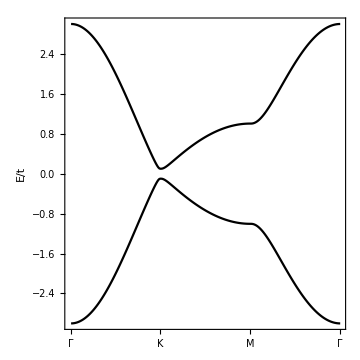

```mathematica
Block[ {m=0.1},ListPlot[Table[ PlotDispData[m][[All,i]],{i,1,2}],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"K"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

### Non-interacting Dtilde

```mathematica
Clear[MassInv];MassInv[m_,k_,dn_] := MassInv[m,k,dn] = Module[ {u = Umat[m,k], D2h = (HamGra[m,k+{dn,0}]+HamGra[m,k-{dn,0}]-2HamGra[m,k])/dn^2},u†.D2h.u];
```

```mathematica
Fermi[β_,x_]:=Chop[N[ 1/(1+ Exp[ β x])]];
```

```mathematica
Clear[Dtilde];Dtilde[m_,dn_,μ_,β_,krange_] := Dtilde[m,dn,μ,β,krange] = 1/Length[kSpan[krange]] Sum[ MassInv[m,k,dn][[band,band]] Fermi[β, Energies[m,k][[band]]-μ],{k,kSpan[krange]},{band,1,2}];
```

```mathematica
Clear[Fill];Fill[m_,dn_,μ_,β_,krange_] := Fill[m,dn,μ,β,krange] = 1/Length[kSpan[krange]] Sum[ Fermi[β, Energies[m,k][[band]]-μ],{k,kSpan[krange]},{band,1,2}];
```

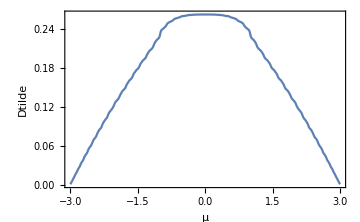

```mathematica
Block[ {m=0.0, dn=0.01, β=100,krange=40}, DiscretePlot[Dtilde[m,dn,μ,β,krange] ,{μ,-3,3,0.01},PlotRange->All,FrameLabel->{"μ","Dtilde"}]]
```

### Pairing Ansatz

The basis is {A,↑,A,↓,B,↑,B,↓}

We consider an orbital diagonal pairing,  Δ_α=-|U| ⟨ d_(iα↑)d_(iα↓) ⟩

```mathematica
DeltaMat[Δ_] :={ {Δ[[1]],0},{0, Δ[[2]]}};
```

```mathematica
Clear[BdGHam];BdGHam[m_,μ_,Δmf_,k_]:= BdGHam[m,μ,Δmf,k]=ArrayFlatten[ {{HamGra[m,k]-μ IdentityMatrix[2], DeltaMat[Δmf]},{DeltaMat[Δmf]†, μ IdentityMatrix[2] - Transpose[HamGra[m,-k]]}}];
```

```mathematica
Clear[BdGEn];BdGEn[m_,μ_,Δmf_,k_] :=BdGEn[m,μ,Δmf,k] =Chop[Sort[ Eigenvalues[ BdGHam[m,μ,Δmf,k] ]]];
```

```mathematica
Clear[BdGU];BdGU[m_,μ_,Δmf_,k_] := BdGU[m,μ,Δmf,k] =N[Transpose[ Transpose[ SortBy[ Transpose[ Eigensystem[ BdGHam[m,μ,Δmf,k] ] ] ,First ] ][[2]]]];
```

#### Gap Equation

```mathematica
Clear[GapEq];GapEq[m_,μ_,Δmf_,krange_] := GapEq[m,μ,Δmf,krange]=1/Length[kSpan[krange]]{Tr[(Sum[ Module[ {U = BdGU[m,μ,Δmf,k],dm =  BdGHam[0.0,0.0,{1,0},Gama]}, U†.dm.U],{k,kSpan[krange]}])[[1;;2,1;;2]]],Tr[(Sum[ Module[ {U = BdGU[m,μ,Δmf,k],dm =  BdGHam[0.0,0.0,{0,1},Gama]}, U†.dm.U],{k,kSpan[krange]}])[[1;;2,1;;2]]]};
```

```mathematica
Clear[NumEq];NumEq[m_,μ_,Δmf_,krange_] := NumEq[m,μ,Δmf,krange]=1+0.5/Length[kSpan[krange]] Tr[(Sum[ Module[ {U =BdGU[m,μ,Δmf,k],dm = KroneckerProduct[PauliMatrix[3], IdentityMatrix[2]]}, U†.dm.U],{k,kSpan[krange]}])[[1;;2,1;;2]]]
```

...Number equation check...

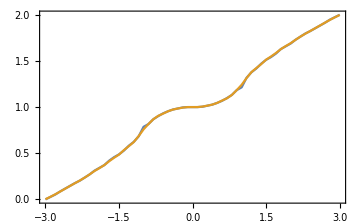

```mathematica
Block[ {m=0.1, Δmf={0,0}, krange=40,dn=0.01,β=100}, DiscretePlot[ {NumEq[m,μ,Δmf,krange],Fill[m,dn,μ,β,krange]},{μ,-3,3,0.1}]]
```

```mathematica
Clear[ItrFnc];ItrFnc[m_,μ_,Δmf_,U_,krange_] :=ItrFnc[m,μ,Δmf,U,krange]= -U GapEq[m,μ,Δmf,krange];
```

```mathematica
Clear[FindΔ];FindΔ[m_,μ_,U_,krange_]:= FindΔ[m,μ,U,krange] = Nest[ ItrFnc[m,μ,#,U,krange]&,RandomReal[{0,U},2],10];
```

```mathematica
FindMuU[m_,fil_,U_,krange_] := FindMuU[m,fil,U,krange] = μ/.FindRoot[ NumEq[m,μ,FindΔ[m,μ,U,krange],krange]-fil,{μ,-3,3},PrecisionGoal->3,Evaluated->False,MaxIterations->10];
```

```mathematica
Clear[FindΔfil];FindΔfil[m_,fil_,U_,krange_]:= FindΔfil[m,fil,U,krange] = FindΔ[m,FindMuU[m,fil,U,krange] ,U,krange];
```

### Gap Equation at Half filling

Check: the number equation should give μ = 0

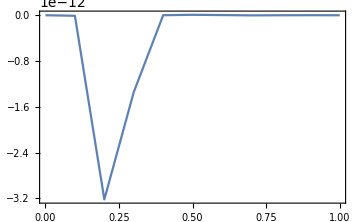

```mathematica
DiscretePlot[FindMuU[0.0,1.0,U,25],{U,0.0,1.0,0.1}]
```

```mathematica
tab = Block[{m=0.0, U=0.1, krange=25},Table[ {fil,Chop[FindΔfil[m,fil,U,krange][[1]]] },{fil,0,2,0.1}]]
```

$Aborted

```mathematica
ListPlot[tab]
```